{a→2.10167×10^-8,b→3.06114}

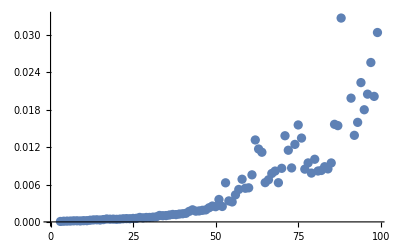

```mathematica
data={
{3,7.07*10^-05},{4,0.0001115},{5,0.0001282},{6,0.0001379},{7,0.0001719},{8,0.0001764},{9,0.0001521},{10,0.0001967},{11,0.0001951},{12,0.0002703},{13,0.0003216},{14,0.0003388},{15,0.0003029},{16,0.000371},{17,0.0004693},{18,0.000435},{19,0.0004436},{20,0.000414},{21,0.0004478},{22,0.0004999},{23,0.0005232},{24,0.0005086},{25,0.0005562},{26,0.0005702},{27,0.0007163},{28,0.0006475},{29,0.000711},{30,0.0007156},{31,0.0007624},{32,0.0008078},{33,0.0010347},{34,0.0009951},{35,0.0010157},{36,0.0011048},{37,0.0011977},{38,0.0011682},{39,0.0012588},{40,0.0013067},{41,0.0013793},{42,0.0016914},{43,0.0019399},{44,0.0017248},{45,0.0017627},{46,0.0018605},{47,0.001927},{48,0.0022659},{49,0.0025429},{50,0.0024404},{51,0.003598},{52,0.0024771},{53,0.006275},{54,0.0033698},{55,0.0032039},{56,0.0043381},{57,0.0052067},{58,0.0068474},{59,0.0054021},{60,0.0054686},{61,0.0075534},{62,0.0131523},{63,0.0117035},{64,0.0111824},{65,0.0063034},{66,0.0067615},{67,0.0077714},{68,0.0081587},{69,0.0062894},{70,0.0086009},{71,0.0138287},{72,0.011504},{73,0.0086623},{74,0.0124414},{75,0.0155626},{76,0.0134573},{77,0.0084655},{78,0.0094689},{79,0.0078343},{80,0.0100538},{81,0.0081704},{82,0.008255},{83,0.0088576},{84,0.0085079},{85,0.0094616},{86,0.0156644},{87,0.0154533},{88,0.032722},{89,0.0563034},{90,0.0392128},{91,0.0198646},{92,0.0138951},{93,0.0159794},{94,0.0223623},{95,0.0180025},{96,0.0205059},{97,0.0255865},{98,0.0201458},{99,0.0304003}
};
line = FindFit[data, a*x^b,{a,b},x]
Show[ListPlot[data], Plot[{line}, {x, 3, 99}]]
```